```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Elastic Collisions in Lab Frame

```mathematica
Solve[{1/2 m vi^2==1/2 m vf^2+1/2 M v^2,m vi==m vf Cos[θ]+M v Cos[ψ],0==m vf Sin[θ]-M v Sin[ψ]},vf,{ψ,v}]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{vf→(2 m vi Cos[θ]-√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))},{vf→(2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))}}

#### Second solution is physical one

```mathematica
Efin=1/2 m((2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M)))^2/.vi->Sqrt[2 ϵ/m];
```

```mathematica
etransfer=FullSimplify[Efin/ϵ,Assumptions->{ϵ>0,M>0,m>0}];
```

```mathematica
1/(2Pi)Integrate[etransfer,{θ,0,2Pi},Assumptions->{ϵ>0,M>0,m>0}]//FullSimplify
```

M^2/(m+M)^2

#### Proper calculation (lab frame angle not exactly isotropic, unlike CM angle) yields ζ= (M^2+m^2)/(m+M)^2~M^2/(m+M)^2for heavy nuclei

```mathematica
ζ=M^2/(m+M)^2;
```

#### How many elastic collisions before lose O(1) of energy?

```mathematica
Solve[ζ^c==0.5/.{M->12000,m->100},c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c→41.7619}}

```mathematica
Solve[ζ^c==0.5/.{M->12000,m->1000},c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c→4.32986}}

```mathematica
dedxelasticmeson=Piecewise[{{ϵ/(50/((n/Z)σ)),ϵ≤10},{0,ϵ>10}}];
dedxelasticnucleon=Piecewise[{{ϵ/(10/((n/Z)σ)),ϵ≤10},{0,ϵ>10}}];
dedxnonelastic=Piecewise[{{ϵ (n/Z σ),ϵ>10},{0,ϵ≤10}}];
```

#### In units of MeV/(10^-5 cm)

```mathematica
Convert[(Mega ElectronVolt)^4 Barn(200 Mega ElectronVolt Fermi)^-2,(Mega ElectronVolt)^2]//N
```

0.0025 ElectronVolt^2 Mega^2

```mathematica
Convert[ElectronVolt^2 Mega^2*(200 Mega ElectronVolt*Fermi)^-1,Mega ElectronVolt/Centimeter]//N
```

(5.×10^10 ElectronVolt Mega)/Centimeter

#### Elastic and Nonelastic stopping powers (σ in barns)

```mathematica
nucleon=LogLogPlot[ReplaceAll[ReplaceAll[dedxnonelastic,{n->8,Z->6}],{σ->0.1,M->12000,m->1000}](0.0025)(5.*^5),{ϵ,10^-1,10^10},PlotLegends->{"Nuclear Nonelastic"},PlotStyle->{Purple,Thick}];
meson=LogLogPlot[ReplaceAll[ReplaceAll[dedxnonelastic,{n->8,Z->6}],{σ->0.1,M->12000,m->140}](0.0025)(5.*^5),{ϵ,10^-1,10^10},PlotLegends->{"Nuclear Nonelastic"},PlotStyle->{Purple,Thick}];
elasticnucleon=LogLogPlot[ReplaceAll[ReplaceAll[dedxelasticnucleon,{n->8,Z->6}],{σ->1,M->12000,m->1000}](0.0025)(5.*^5),{ϵ,1,10^10},PlotLegends->{"Nuclear Elastic"},PlotStyle->{Cyan,Thick}];
elasticmeson=LogLogPlot[ReplaceAll[ReplaceAll[dedxelasticmeson,{n->8,Z->6}],{σ->1,M->12000,m->140}](0.0025)(5.*^5),{ϵ,1,10^10},PlotLegends->{"Nuclear Elastic"},PlotStyle->{Cyan,Thick}];
```

#### Canvases for stopping power plots

```mathematica
canvasphoton=LogLogPlot[10^20,{ϵ,1,10^8},Frame->True,PlotRange->{1,10^7},FrameLabel->{"Photon Energy (MeV)","Stopping Power (MeV/10^-5cm)"},LabelStyle-> Directive[Bold]];
canvasnucleon=LogLogPlot[10^20,{ϵ,1,10^7},Frame->True,PlotRange->{1,10^7},FrameLabel->{"Nucleon Energy (MeV)","Stopping Power (MeV/10^-5cm)"},LabelStyle-> Directive[Bold]];
canvaspion=LogLogPlot[10^20,{ϵ,1,10^7},Frame->True,PlotRange->{1,10^9},FrameLabel->{"Pion Energy (MeV)","Stopping Power (MeV/10^-5cm)"},LabelStyle-> Directive[Bold]];
canvaselectron=LogLogPlot[10^20,{ϵ,1,10^8},Frame->True,PlotRange->{10^-3,10^7},FrameLabel->{"Electron Energy (MeV)","Stopping Power (MeV/10^-5cm)"},LabelStyle-> Directive[Bold]];
```

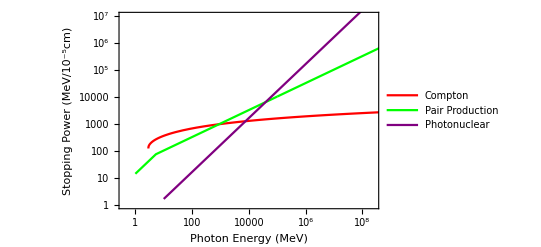

```mathematica
photonall=Show[canvasphoton,compton,photonpp,electronbremalpha,photonhad]
```

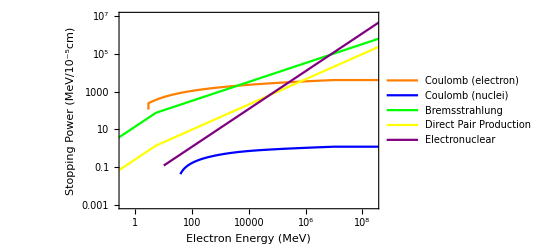

```mathematica
electronall=Show[canvaselectron,electronpauli,electronpauliflat,electron,electronflat,electronbrem,electronbremalpha,electrondpp,electronhad]
```

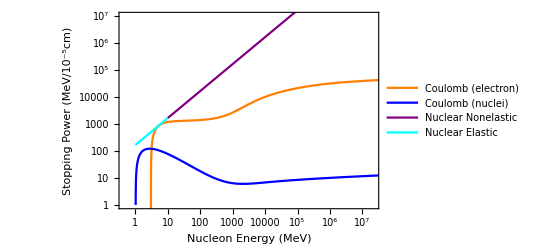

```mathematica
nucleonall=Show[canvasnucleon,protonpauli,proton,nucleon,elasticnucleon]
```

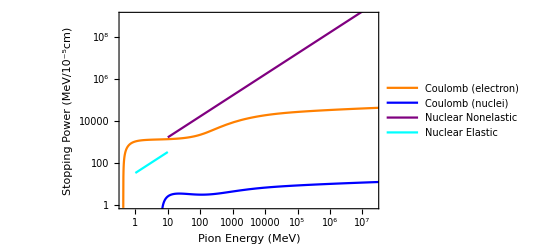

```mathematica
pionall=Show[canvaspion,pionpauli,pion,meson,elasticmeson]
```

```mathematica
Export["/Users/NewUser/Documents/Qballs/SPphoton.pdf",photonall];
Export["/Users/NewUser/Documents/Qballs/SPelectron.pdf",electronall];
Export["/Users/NewUser/Documents/Qballs/SPpion.pdf",pionall];
Export["/Users/NewUser/Documents/Qballs/SPnucleon.pdf",nucleonall];
```

#### $$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$

#### Hadrons

#### Shower length

```mathematica
showerlength=Convert[Integrate[ReplaceAll[dedxnonelastic^-1,{α->1/137,M->12000,Z->6,n->8,m->1000,σ->0.1}],{ϵ,10,ϵ},Assumptions->{ϵ>10}] 1/((Mega ElectronVolt)^3 Barn)*(200 Mega ElectronVolt*Fermi)^3,Centimeter] 1/Centimeter;
```

#### Final-state nucleons - elastic scattering in the form of a random walk

```mathematica
finalnucleon=Convert[1/(n*σ)*Sqrt[10]/.{n->10^32 Centimeter^-3,σ->1Barn},Centimeter] 1/Centimeter;
```

```mathematica
finalpion=Convert[1/(n*σ)*Sqrt[80]/.{n->10^32 Centimeter^-3,σ->0.1Barn},Centimeter] 1/Centimeter;
```

```mathematica
{showerlength,finalnucleon,finalpion}/.ϵ->500//N
```

{2.34721×10^-7,3.16228×10^-8,8.94427×10^-7}

```mathematica
Lhadron=LogLogPlot[showerlength+Max[finalnucleon,finalpion],{ϵ,10^6,10^18},PlotStyle->{Blue,Thick}];
```

```mathematica
canvasL=LogLogPlot[10^20,{ϵ,10^7,10^17},Frame->True,PlotRange->{5 10^-7,10^-3},FrameLabel->{"Incident Energy ϵ (MeV)","L_i(cm)"},PlotLabel->"Individual Heating Lengths for SM species"];
```

#### Electrons and Photons

```mathematica
brem
```

Piecewise[{{(√(Elpm/ϵ) ϵ)/X0, Elpm≤ϵ≤m^4/(16 n π Z α^4)}, {ϵ/X0, ϵ≤Elpm}, {0, True}}]

```mathematica
Integrate[((√(Elpm/ϵ) ϵ)/X0)^-1,{ϵ,ϵc,ϵ},Assumptions->{ϵ>0,ϵc>0}]
```

ConditionalExpression[(2 X0 (√ϵ-√ϵc))/(√Elpm),ϵ>ϵc]

```mathematica
Integrate[((10 n α ϵ σγ)/Z)^-1,{ϵ,ϵ/2,ϵ},Assumptions->{ϵ>0}]
```

(Z Log[2])/(10 n α σγ)

```mathematica
electroninitial=Convert[(Z Log[2])/(10 n α σγ)/.{Z->6,n->10^33 Centimeter^-3,α->1/137,σγ->1 Milli Barn},Centimeter] 1/Centimeter;
```

```mathematica
photoninitial=Convert[(Z Log[2])/(n σγ)/.{Z->6,n->10^33 Centimeter^-3,α->1/137,σγ->1 Milli Barn},Centimeter] 1/Centimeter;
```

```mathematica
Lphoton=LogLogPlot[photoninitial+showerlength+Max[finalnucleon,finalpion],{ϵ,10^6,10^18},PlotStyle->{Yellow,Thick}];
```

```mathematica
Lelectron=LogLogPlot[electroninitial+showerlength+Max[finalnucleon,finalpion],{ϵ,10^6,10^18},PlotStyle->{Red,Thick}];
```

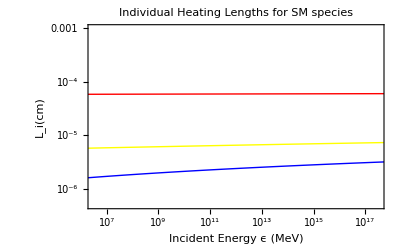

```mathematica
Show[canvasL,Lphoton,Lelectron,Lhadron]
```